```mathematica
n=100;  (*max capital (0 is not used)*)


p=0.4;(* # The probability of the coin coming up heads.*)
V=Table[0.0,{i,0,n}]; (*# containing two dummy states V[0]=0 and V[N]=1*)
aopt=Table[0,{i,1,n-1}];
V[[n+1]]=1.0;(* # win if he has 100 stakes*)
isStable=False;
minError=1 10^-25;
gamma=1.0;
sweep=0;
delta=Table[0,{10000}];

While[isStable==False&&sweep<100,
{
sweep=sweep+1;
delta[[sweep]]=0;
isStable = True;
Do[
{
Vpre=V[[s+1]];
Vtmp=Table[0,{a,0,n-1}];
Do[
{
Vtmp[[a+1]]=p*gamma*V[[s+a+1]]+(1.0-p)*gamma *V[[s-a+1]];
},{a,0,Min[s,n-s]}];
Vtmp2=Vtmp[[2;;n]];
m=Max[Vtmp2];
aopt[[s]]=Position[Vtmp2,m][[1,1]];
V[[s+1]]=m;
delta[[sweep]]=Max[Abs[Vpre-V[[s+1]]],delta[[sweep]]];
If[Abs[Vpre-V[[s+1]]]>minError,isStable=False]
},{s,1,n-1}];
}
]
```

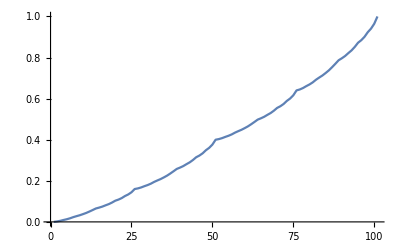

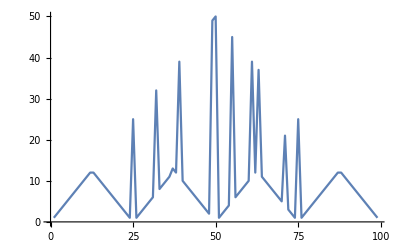

```mathematica
ListLinePlot[V]
ListLinePlot[aopt,PlotRange->Full]
```

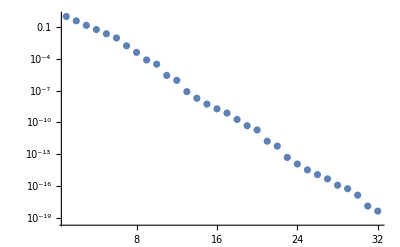

```mathematica
ListLogPlot[delta,PlotRange->All]
```